# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\QMB_offline.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# <r>

```mathematica
δ=7;
J=1;
glist=Table[10^i,{i,-3,0,0.01}];
hlist=Table[10^i,{i,-3,0,0.01}];
```

```mathematica
Do[

basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];

DistributeDefinitions[IsingNNOpenHamiltonian,Beven,Bodd];
SetSharedVariable[data];
data={};
ParallelDo[
	Module[{H, eigenvals,Heven,Hodd,eveneigenval,oddeigenval},
H = IsingNNOpenHamiltonian[1,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
eveneigenval=Sort[Eigenvalues[N[Heven]]];
oddeigenval=Sort[Eigenvalues[N[Hodd]]];
AppendTo[data,{{g,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{g,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {g,glist}
, Method->"CoarsestGrained"];
Export["r_L_"<>ToString[L]<>"_h_1_log_g.m",Sort[data]];

DistributeDefinitions[IsingNNOpenHamiltonian,Beven,Bodd];
SetSharedVariable[data];
data={};
ParallelDo[
	Module[{H, eigenvals,Heven,Hodd,eveneigenval,oddeigenval},
H = IsingNNOpenHamiltonian[h,1,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
eveneigenval=Sort[Eigenvalues[N[Heven]]];
oddeigenval=Sort[Eigenvalues[N[Hodd]]];
AppendTo[data,{{h,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{h,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {h,hlist}
, Method->"CoarsestGrained"];
Export["r_L_"<>ToString[L]<>"_g_1_log_h.m",Sort[data]];

,{L,6,8,1}]
```

# Results

## g

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_14_g_1_log_h.m"];
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

```mathematica
L=14;
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

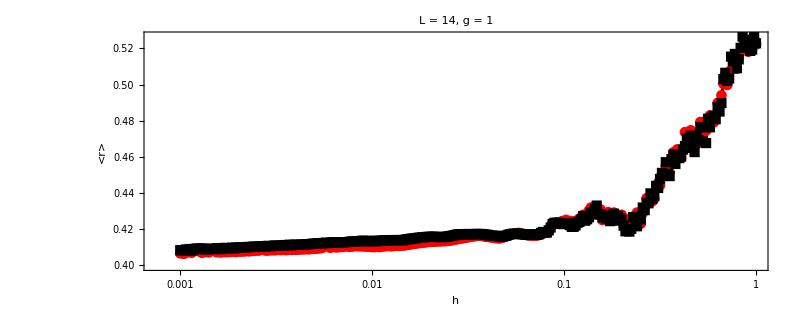

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

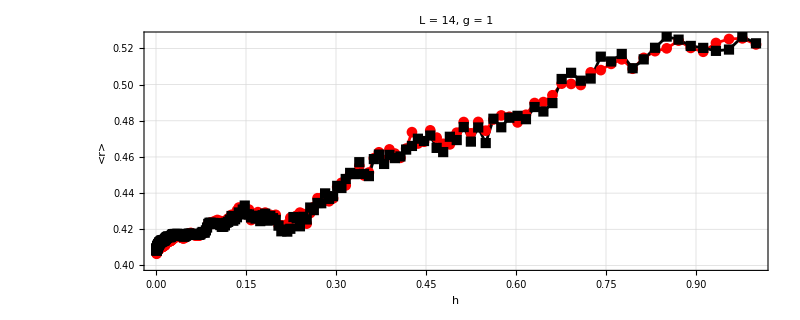

```mathematica
ListLogLinearPlot[{Sort[data[[All,1]]],Sort[data[[All,2]]]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
ListPlot[{Sort[data[[All,1]]],Sort[data[[All,2]]]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_14_h_1_log_g.m"];
```

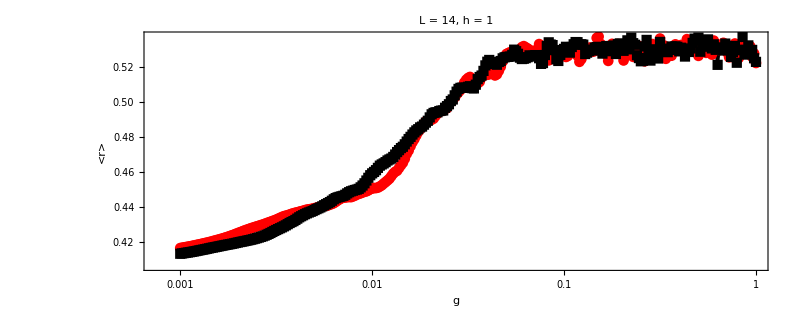

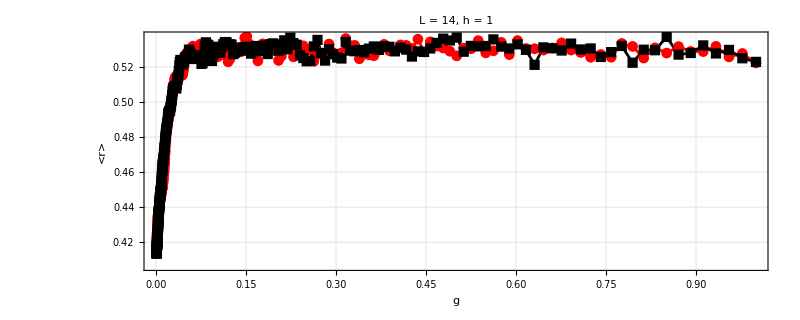

```mathematica
ListLogLinearPlot[{Sort[data[[All,1]]],Sort[data[[All,2]]]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
ListPlot[{Sort[data[[All,1]]],Sort[data[[All,2]]]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

## previous

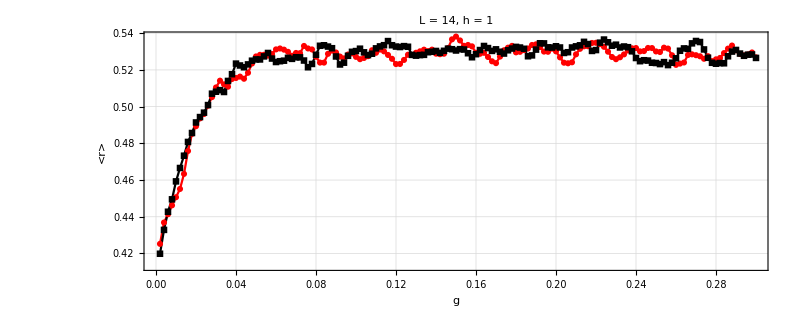

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

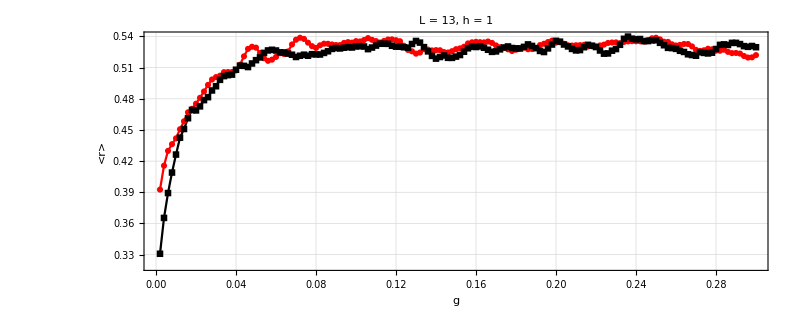

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

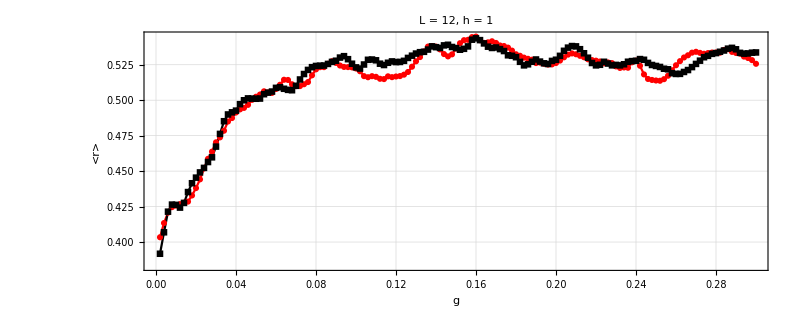

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

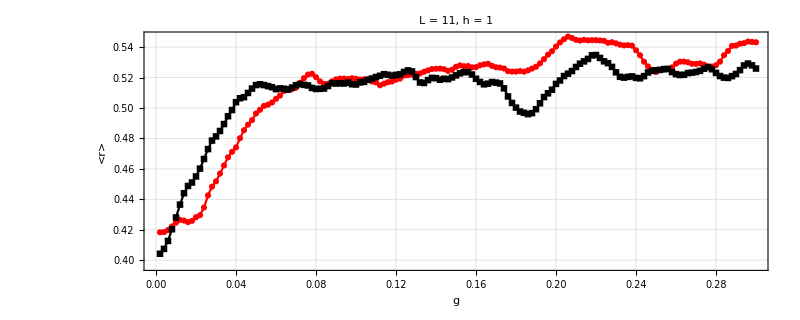

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

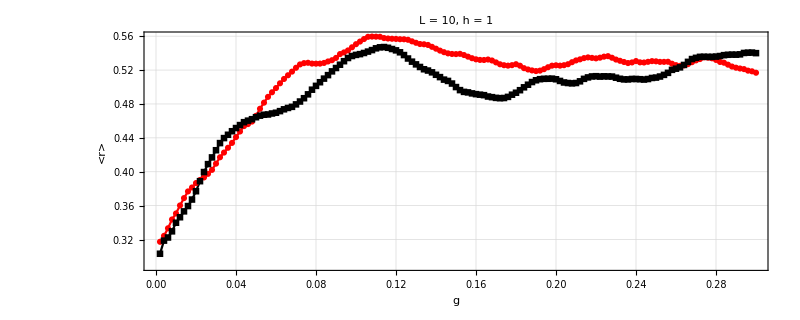

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

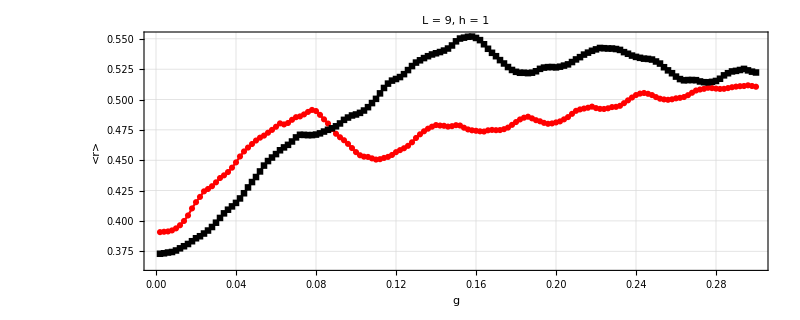

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

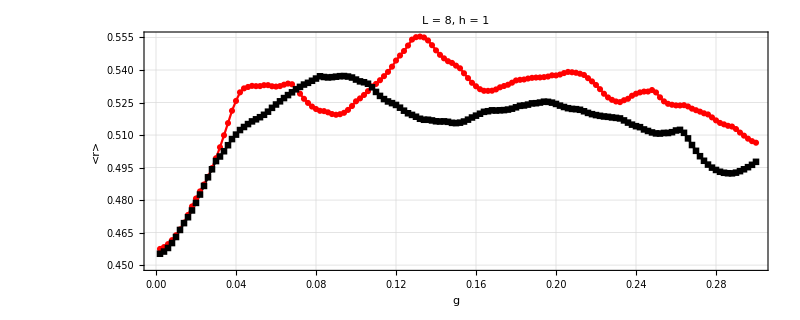

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

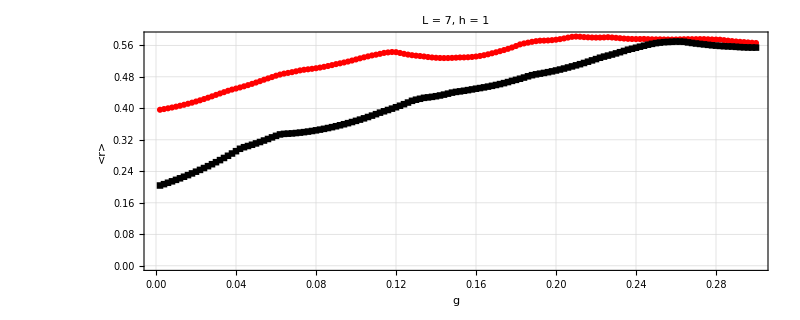

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

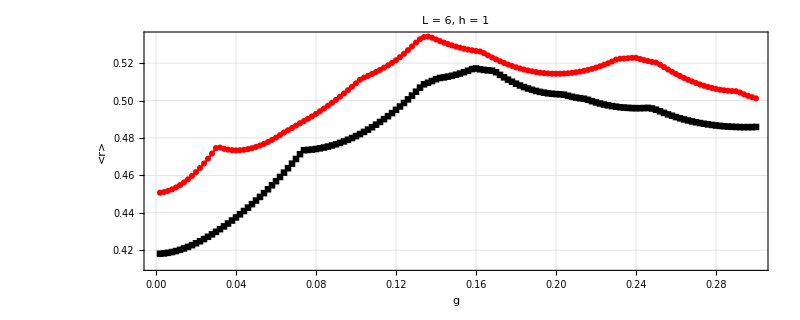

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

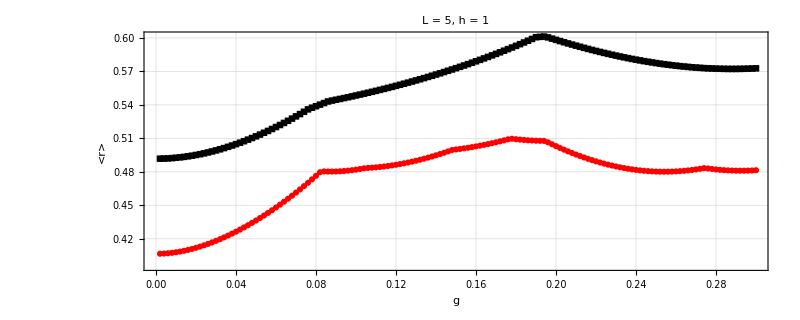

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

## h

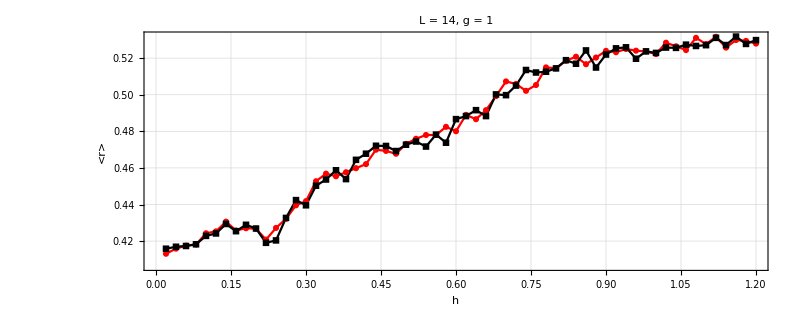

```mathematica
ListPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```

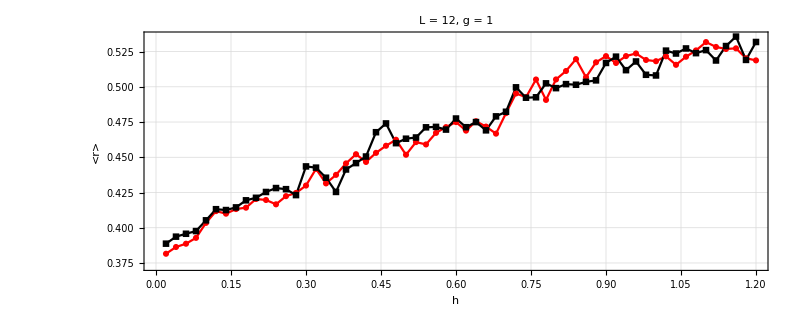

```mathematica
ListPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```

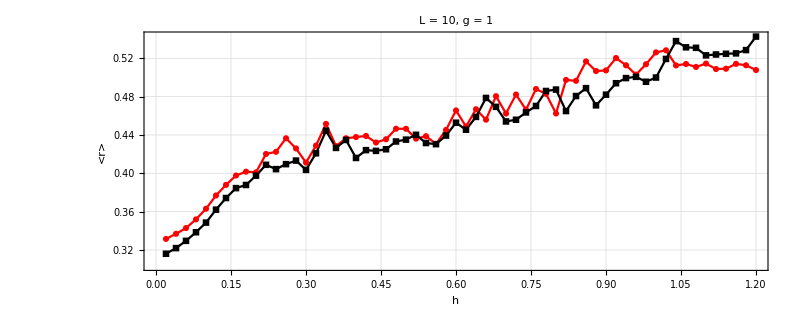

```mathematica
ListPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```

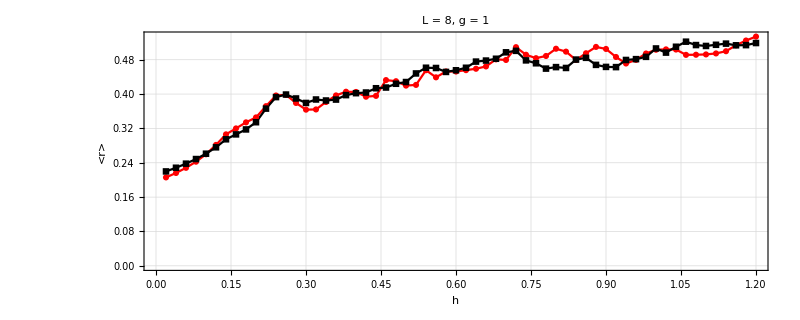

```mathematica
ListPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```

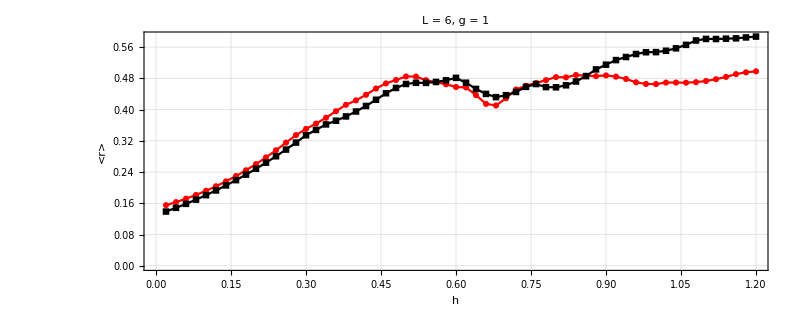

```mathematica
ListPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black]]
```

```mathematica
g=0.02;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

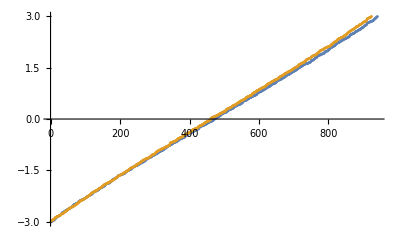

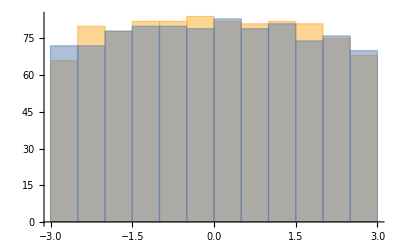

0.445718

0.453809

```mathematica
δ=3;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]},10]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
```

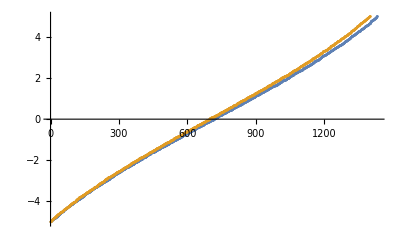

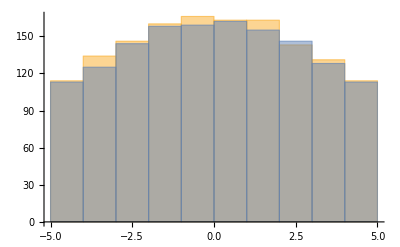

0.444391

0.446133

```mathematica
δ=5;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]},10]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
```

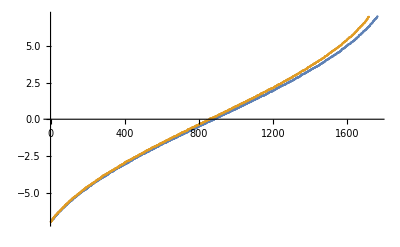

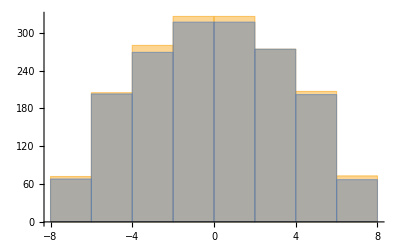

0.440306

0.444022

```mathematica
δ=7;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]},10]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
```

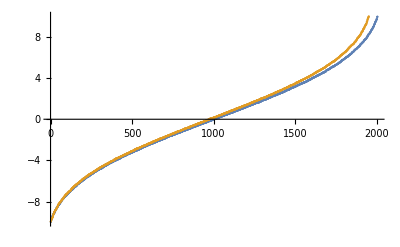

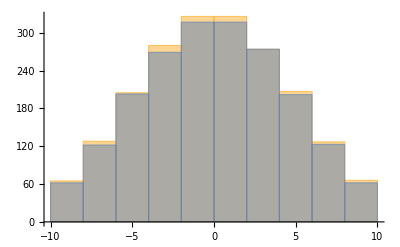

0.438992

0.446749

```mathematica
δ=10;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]},10]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
```

## Spectrum

```mathematica
L=10;
```

```mathematica
J=1;
h=0.1;
g=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
(*Generate the computational basis (list of bit strings)*)
basis=Tuples[{0,1},L];
(*The basis will contain 16 elements,each representing a state|s1,s2,s3,s4>*)
(*Convert a given binary state (list) to an integer index*)
ToIndex[state_List]:=FromDigits[state,2]+1;
(*For each basis state,find the index of its reflection*)
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
(*Convert the mapping into a permutation cycles object*)
permCycles=PermutationCycles[permutation];
(*Construct the reflection symmetry operator as a 16x16 permutation matrix*)
R=PermutationMatrix[permCycles,2^L];
```

```mathematica
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
```

```mathematica
(*Form the change-of-basis matrix for the even sector*)
Beven=Transpose[evenBasis];
(*The projected even sector Hamiltonian is then:*)
Heven=ConjugateTranspose[Beven].H.Beven;
(*Similarly for the odd sector*)
Bodd=Transpose[oddBasis];
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
(*Peven=ConjugateTranspose[Beven].N[R].Beven;
Podd=ConjugateTranspose[Bodd].R.Bodd;*)
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[Heven]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[Hodd]]]];
```

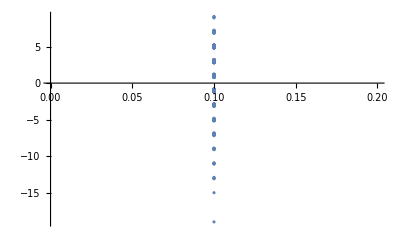

```mathematica
Transpose[{ConstantArray[0.1,Length[eveneigenval]],eveneigenval}]//ListPlot
```

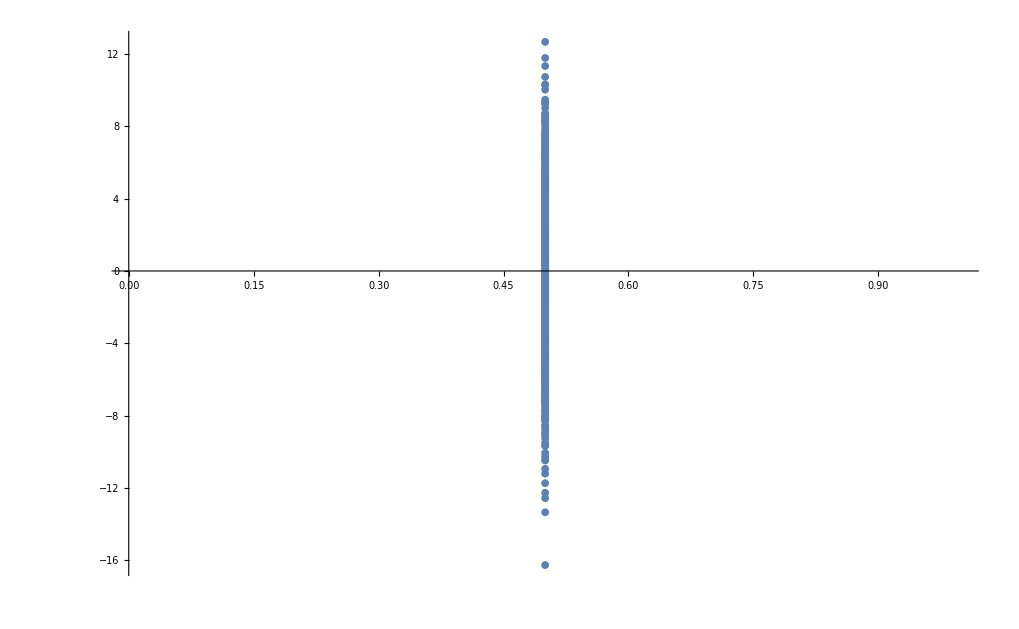

```mathematica
Transpose[{ConstantArray[0.5,Length[eveneigenval]],eveneigenval}]//ListPlot
```

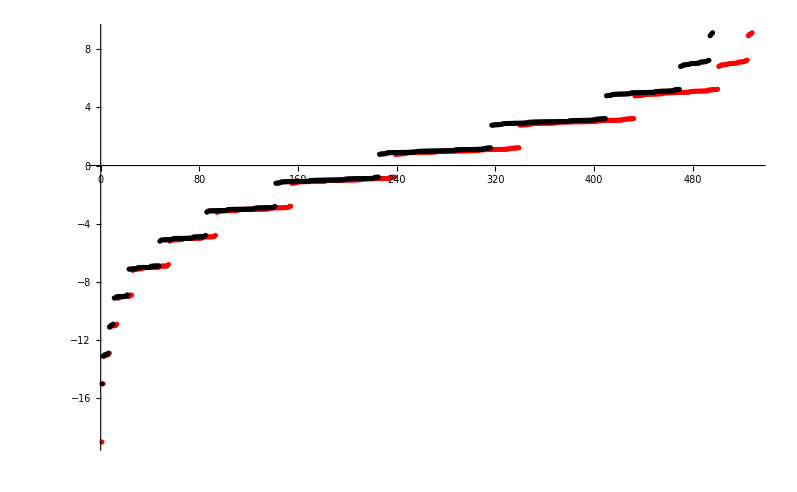

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All,PlotStyle->{Red,Black}]
```

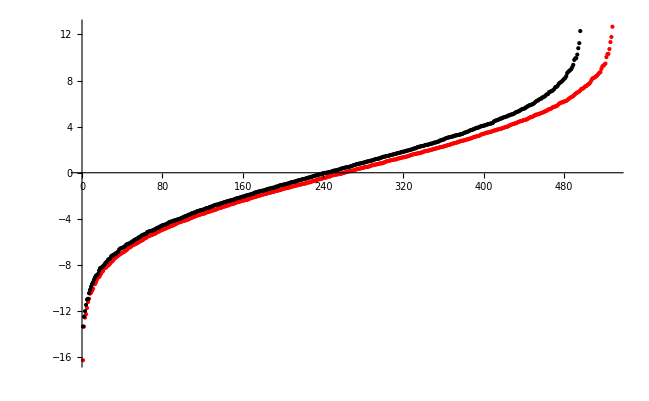

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All,PlotStyle->{Red,Black}]
```

```mathematica
MeanLevelSpacingRatio[eveneigenval]
MeanLevelSpacingRatio[oddeigenval]
```

0.526817

0.52442

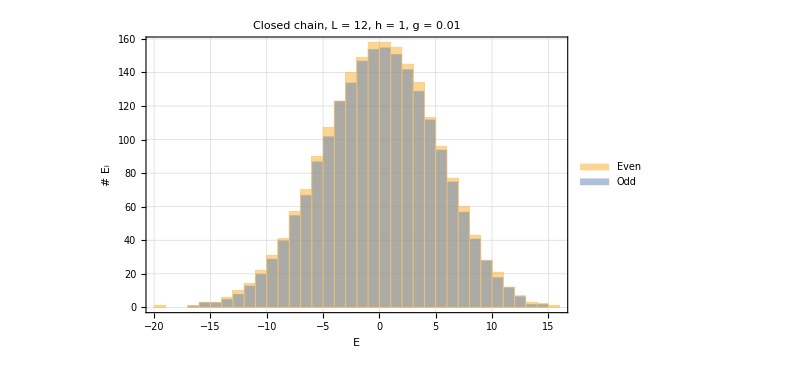

```mathematica
Histogram[{eveneigenval,oddeigenval},PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["Closed chain, L = 12, h = 1, g = 0.01",30,Black],FrameLabel->{Style["E",30,Black],Style["# E_i",30,Black]},FrameStyle->{{25,Black},{25,Black}},ChartLegends->{Style["Even",25,Black],Style["Odd",25,Black]}]
```

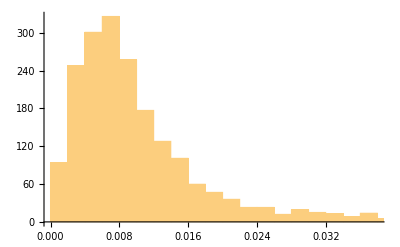

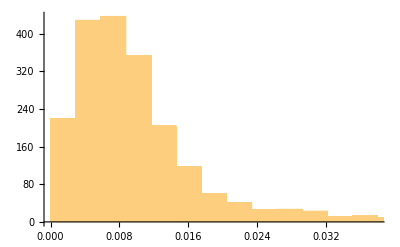

```mathematica
Histogram[Differences[oddeigenval]]
Histogram[Differences[eveneigenval]]
```

```mathematica
evenrelative=Table[(eveneigenval[[i+1]]-eveneigenval[[i]])/(eveneigenval[[i+1]]+eveneigenval[[i]]),{i,Length[eveneigenval]-1}];
```

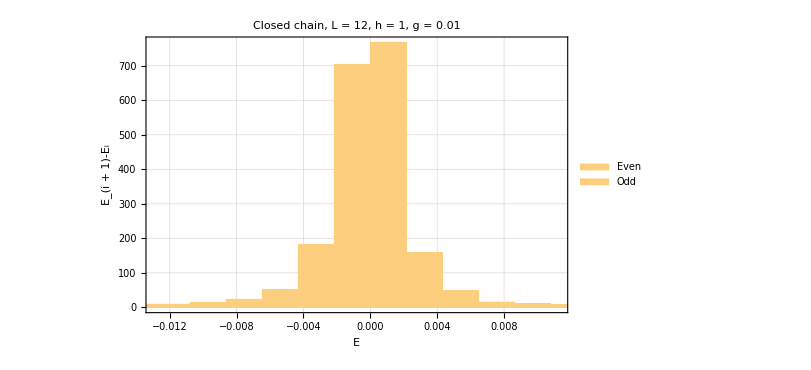

```mathematica
Histogram[evenrelative,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["Closed chain, L = 12, h = 1, g = 0.01",30,Black],FrameLabel->{Style["E",30,Black],Style["E_(i + 1)-E_i",30,Black]},FrameStyle->{{25,Black},{25,Black}},ChartLegends->{Style["Even",25,Black],Style["Odd",25,Black]}]
```

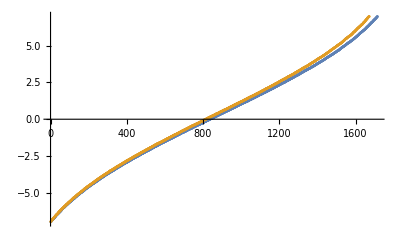

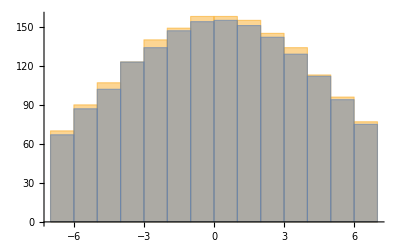

0.525925

0.526574

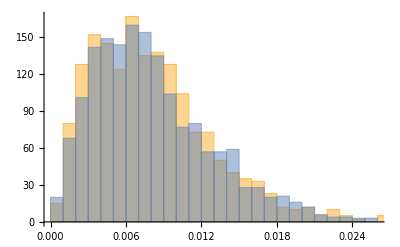

```mathematica
δ=7;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
Histogram[{Differences[Select[eveneigenval,-δ<=#<=δ&]],Differences[Select[oddeigenval,-δ<=#<=δ&]]}]
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

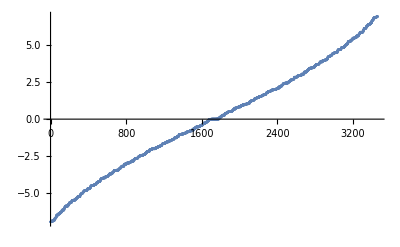

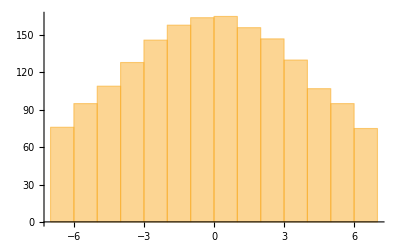

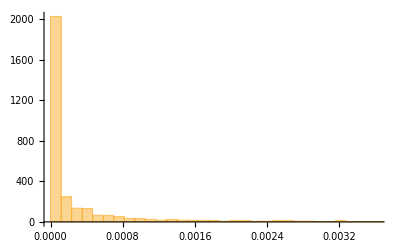

```mathematica
δ=7;
ListPlot[{Select[eigenval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&]}]
Histogram[{Differences[Select[eigenval,-δ<=#<=δ&]]}]
```